## Checking r

```mathematica
(*Subscript[h, x]: magnetic field in x direction. L: number of spins*)
{hx,L}={1,11}
```

{1,11}

```mathematica
{hz,J}={0.01,0.32};
H=IsingNNOpenHamiltonian[hx,hz,ConstantArray[J,L-1],L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
```

```mathematica
{EvenEigVals,evenEigenVecs}={eigVals[[#]],eigVecs[[#]]}&[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]];
OddEigVals=Complement[eigVals,EvenEigVals];
OddEigVecs=Complement[eigVecs,evenEigenVecs];
{MeanLevelSpacingRatio[OddEigVals],MeanLevelSpacingRatio[EvenEigVals]}
```

{0.312133,0.282751}

```mathematica
pm=ParityMatrix[L];
```

```mathematica
AllTrue[Braket[#,pm.#]&/@ParityEigenvectors[L][[2]],#==-1&]
```

$Aborted

```mathematica
AbsoluteTiming[{eveneigenvecs,oddeigenvecs}=ParityEigenvectors[L];]
```

{0.465775,Null}

```mathematica
AllTrue[Braket[#,pm.#]&/@eveneigenvecs,#==1&]
```

True

```mathematica
AbsoluteTiming[Heven=Table[Chop[Conjugate[H.i].#&/@eveneigenvecs],{i,eveneigenvecs[[1;;2]]}];]
```

{3.30071,Null}

```mathematica
1.65*1000/60
```

27.5

```mathematica
AbsoluteTiming[bra=Conjugate[H.#]&/@eveneigenvecs;]
```

{1.3257,Null}

```mathematica
AbsoluteTiming[bra=ParallelMap[Conjugate[H.#]&,eveneigenvecs];]
```

{1.77524,Null}

```mathematica
AbsoluteTiming[Heven=Table[Map[i.#&,eveneigenvecs],{i,bra}];]
```

{6.45412,Null}

```mathematica
(*Los eigenvalores de Heven están en eigvals*)
Complement[Round[Eigenvalues[Heven],10.^-6],Round[eigVals,10.^-6]]
```

{}

```mathematica
Complement[Round[Eigenvalues[Heven],10.^-6],Round[EvenEigVals,10.^-6]]
Intersection[Round[Eigenvalues[Heven],10.^-6],Round[EvenEigVals,10.^-6]]//Length
```

{}

1056

```mathematica
MeanLevelSpacingRatio[Sort[Eigenvalues[Heven]]]
```

0.282751

## Checking IPR of eigenvectors

```mathematica
evenEigenVecs//Dimensions
```

{1056,2048}

```mathematica
iprseven=ParallelTable[Total[Abs[i]^4],{i,evenEigenVecs}];
```

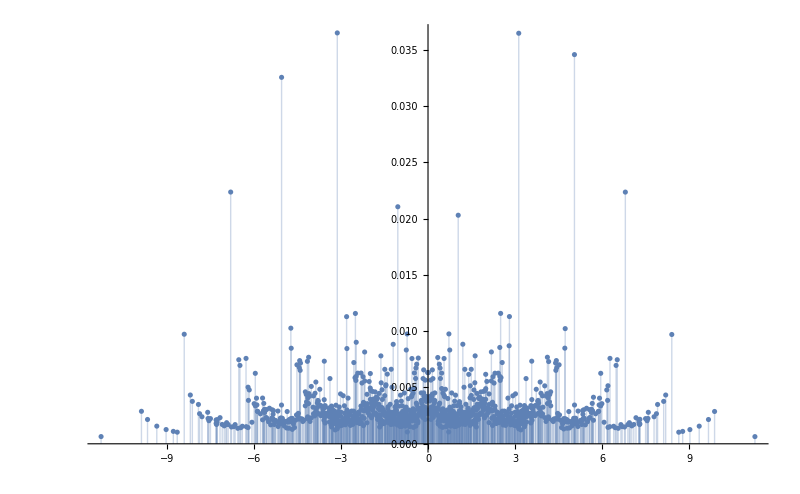

```mathematica
ListPlot[Transpose[{EvenEigVals,iprseven}],PlotRange->All,Filling->Axis,ImageSize->800]
```

```mathematica
1/1056.
```

0.00094697

```mathematica
MeanLevelSpacingRatio[EvenEigVals[[Flatten[Position[iprseven,x_/;x<=0.005]]]]]
```

0.297209

## Checking commutativity with

```mathematica
L=11;
```

```mathematica
{hz,J}={0.01,0.32};
H=IsingNNOpenHamiltonian[hx,hz,ConstantArray[J,L-1],L];
```

```mathematica
totalmz=Total[Pauli/@(3*IdentityMatrix[L])]
```

SparseArray[…]

```mathematica
CommutationQ[H,totalmz]
```

False

```mathematica
totalmagnetization=Total[Table[Total[Pauli/@(i*IdentityMatrix[L])],{i,3}]]
```

SparseArray[<24576>, {2048, 2048}]

```mathematica
CommutationQ[H,totalmagnetization]
```

False